#### Referência: - pacote mdgp.nb ( goo.gl/KE9WSM )

Instance Creation
DGAllEdges, DGEdgeWeight, DGEdgeDistanceBounds, DGProblem, DGGraphGetIJD, DGSetXByCartesianSystem, DGSetXByHomogeneousCoords, DGRandom3DBackbone, DGRandomMDGP

## Source Code

```mathematica
ClearAll[
DGAllEdges,
DGEdgeWeight,
DGEdgeDistanceBounds,
DGProblem,
DGPrintGraph,
DGPrintX,
DGGraphGetIJD,
DGSetXByCartesianSystem,
DGSetXByHomogeneousCoords,
DGRandom3DBackbone
  ];

DGAllEdges[n_] := Module[{i, j, k = 0, pij},
   pij = Table[0, {i, (n (n - 1))/2}];
   For[i = 1, i <= n, i++,
    For[j = (i + 1), j <= n, j++,
      k++;
      pij[[k]] = i <-> j;
      ];
    ];
   Return[pij]
   ];

DGEdgeWeight[G_, E_] :=
  (* Gets edge weight. 'E' can be a single edge or a list of edges; *)
  Module[
{i, eij,wij, D = {}},
If[Not[FailureQ[PropertyValue[{G, E[[1]]}, EdgeWeight]]],
(* E is a list of edges *)
For[i = 1, i <= Length[E], i++,
eij = E[[i]];
If[eij[[1]] > eij[[2]], eij = eij[[2]] <-> eij[[1]]];
If[FailureQ[wij=PropertyValue[{G, eij}, EdgeWeight]],Throw[{"InvalidEdge:",eij}]];
AppendTo[D, wij]],
(* E is a single edge *)
eij = E;
If[eij[[1]] > eij[[2]], eij = eij[[2]] <-> eij[[1]]];
If[FailureQ[D = PropertyValue[{G, E}, EdgeWeight]],Throw[{"InvalidEdge:",eij}]]
];
Return[D]
];

DGEdgeDistanceBounds[G_, E_] := Module[
   {eij = E, Lij, Uij, Vij},
   If[eij[[1]] > eij[[2]], eij = eij[[2]] <-> eij[[1]]];
   Vij = PropertyValue[{G, eij}, "DistanceBounds"];
   Return[Vij]
   ];

DGProblem[x_,eij_: {},dijEps_: {}] :=
  (* Creates a problem P such that P["G"] is the problem graph and P["X"] is a problem solution; *)
  Module[{i,j,d,dij,k,numberOfAtoms,G,E,DijEps},
   (* set default values *)
   If[Length[eij]>0,E=eij,E=DGAllEdges[Length[x]]];
   If[Length[dijEps]>0,DijEps=dijEps,DijEps=Table[0,{i,Length[E]}]];
   (* unpacks the edges and calculate distances *)
   i=Table[E[[k]][[1]],{k,Length[E]}];
   j=Table[E[[k]][[2]],{k,Length[E]}];
   d=Table[N[Norm[x[[i[[k]]]] - x[[j[[k]]]]]], {k, Length[E]}];
   numberOfAtoms = Max[i, j];
   (* creates distance matrix *)
   G=Table[Infinity, {i, 1, numberOfAtoms}, {j, 1, numberOfAtoms}];
   For[k=1,k≤Length[i],k++,
      G[[i[[k]]]][[j[[k]]]]=d[[k]];
      G[[j[[k]]]][[i[[k]]]]=d[[k]]
    ];
   (* creates the graph *)
   G = WeightedAdjacencyGraph[G];
   (* adds distance bounds *)
   If[Length[DijEps]!=Length[i],Throw["InvalidInput: eij and dijEps must have the same size"]]; 
   For[k=1,k≤Length[i],k++,
    dij=DGEdgeWeight[G,i[[k]]<->j[[k]]];
    PropertyValue[{G,i[[k]]<->j[[k]]},"DistanceBounds"]={(1-DijEps[[k]]),(1+DijEps[[k]])}*dij
    ];
   Return[<|"X"->x,"G"->G|>]
   ];

DGPrintGraph[G_]:=Module[{edges,table,eij,i,j,k,Lij,Uij,Dij},
edges=EdgeList[G];
table=Table[0,{i,Length[edges]},{j,5}];
For[k=1,k≤Length[edges],k++,
eij=edges[[k]];
{i,j}={eij[[1]],eij[[2]]};
{Lij,Uij}=DGEdgeDistanceBounds[G,eij];
Dij=DGEdgeWeight[G,eij];
table[[k]]={i,j,Dij,Lij,Uij}
];
Print[TableForm[table,TableHeadings->{Table[i,{i,Length[edges]}],{"i","j","dij","lij","uij"}}]]
];

DGPrintX[X_]:=Print[TableForm[X, TableHeadings -> {Table[i, {i, Length[X]}], {"x", "y", "z"}}]]; 

DGPrintDistanceMatrix[X_,edges_]:=Module[{E=edges,table,i,j,k},
table=Table[{i=E[[k]][[1]],j=E[[k]][[2]],N[Norm[X[[i]]-X[[j]]]]},{k,Length[E]}];
Print[TableForm[table,TableHeadings->{Table[i,{i,Length[E]}], {"i","j","dij"}}]]
];
DGPrintDistanceMatrix[X_]:=Module[{edges},
edges=DGAllEdges[Length[X]];
DGPrintDistanceMatrix[X,edges]
];

DGGraphGetIJD[G_]:=Module[{i,j,k,d,E},
E=EdgeList[G];
i=Table[E[[k]][[1]],{k,Length[E]}];
j=Table[E[[k]][[2]],{k,Length[E]}];
d=Table[DGEdgeWeight[G,E[[k]]],{k,Length[E]}];
Return[{i,j,d}];
]

DGSetXByCartesianSystem[d_,θ_,ω_]:=
(* Calculates Euclidean coords from distances, planar and dihedral angles using rotations and translations explicitly;
   Input parameters;
   d: distances       (d[i] = norm(x[[i]]-x[[i-1]]));            
   θ: planar angles   (θ[i] = angle(x[i],x[i-1],x[i-2]));        
   ω: dihedral angles (ω[i] = angle(x[i],x[i-1],x[i-2],x[i-3]) 
*)
Module[
(* declare local variables *)
{a,b,c,i,v,n,R,X,numberOfAtoms},
numberOfAtoms=Length[d];
(* atoms positions on Euclidean 3d space *)
X=Table[0,{i,numberOfAtoms},{j,3}];
(* set the position of the three first points *)
X[[{1,2,3}]]={{0,0,0},{-d[[2]],0,0},{-d[[2]]+d[[3]]Cos[θ[[3]]],d[[3]]Sin[θ[[3]]] ,0}};
(* set remaining positions *)
For[i=4,i≤numberOfAtoms,i++,
{a,b,c}={X[[i-3]],X[[i-2]],X[[i-1]]};
v= d[[i]]* Normalize[b-c]; 
(* normal to the plane abc *)
n=Cross[a-b,c-b];
(* apply plane rotation *)
R=RotationTransform[θ[[i]],n]; (* rotation creation *)
v=R[v]; (* rotation apply *)
(* apply torsion rotation and translation *)
R=RotationTransform[ω[[i]],c-b];
v=R[v]+c;
(* set i-th coordinate *)
X[[i]]=v
];
Return[X]
];

DGSetXByHomogeneousCoords[d_,θ_,ω_]:=
(* Calculates Euclidean coords from distances, planar and dihedral angles using transformation matrices;
   Input parameters;
   d: distances       (d[i] = norm(x[[i]]-x[[i-1]]));            
   θ: planar angles   (θ[i] = angle(x[i],x[i-1],x[i-2]));        
   ω: dihedral angles (ω[i] = angle(x[i],x[i-1],x[i-2],x[i-3]); 
*)
Module[
{B,B1,B2,B3,X,i,di,ct,st,cw,sw,v,numberOfAtoms},
numberOfAtoms=Length[d];
(* atoms positions on Euclidean 3d space *)
X=Table[0,{i,numberOfAtoms},{j,3}];
(* set the position of the three first points *)
{ct,st}={Cos[θ[[3]]],Sin[θ[[3]]]};
X[[{1,2,3}]]={{0,0,0},{-d[[2]],0,0},{-d[[2]]+d[[3]]ct,d[[3]]st ,0}};
(* set first transformation matrices *)
B1=IdentityMatrix[4];
B2={{-1,0,0,-d[[2]]},{0,1,0,0},{0,0,-1,0},{0,0,0,1}};
di=d[[3]];
B3={{-ct,-st,0,-di*ct},{st,-ct,0,di*st},{0,0,1,0},{0,0,0,1}};
(* set remaining coordinates *)
B=B1.B2.B3;
For[i=4,i≤numberOfAtoms,i++,
{ct,st}={Cos[θ[[i]]],Sin[θ[[i]]]};
{cw,sw}={Cos[ω[[i]]],Sin[ω[[i]]]};
di=d[[i]];
(* concatenate transformation matrices *)
B =B.{{-ct,-st,0,-di*ct},{st*cw,-ct*cw,-sw,di*st*cw},{st*sw,-ct*sw,cw,di*st*sw},{0,0,0,1}};
(* apply transformation at origin *)
v =B.{0,0,0,1};
(* update coordinate *)
X[[i]]=v[[{1,2,3}]];
];
Return[X]
];

DGRandom3DBackbone[numberOfAtoms_,algorithm_:"HomogeneousCoords",seed_:0]:=
(* Generates a random backbone in tridimensional Euclidean space;
   Input parameters;
   numberOfAtoms: number of 3D Euclidean points to be generated;
   algorithm: algorithm to be applied during coordinates calculation. The options 'are HomogeneousCoords' or 'CartesianSystem';
   seed: integer number used to reproduce random sequence generation. If seed=0 a sequence based on the current time is constructed;
 *)
Module[
(* declare the local variables *)
{d,θ,ω,X,output,ϵ=0.05},
(* set seed *)
If[seed>0,SeedRandom[seed]];
(* length of covalent bonds *)
d=Table[1.526,{i,numberOfAtoms}];
d[[1]]=0;
(* plane angles *)
θ=Table[1.91,{i,numberOfAtoms}];
θ[[{1,2}]]={0,0};
(* torsion angles *)
ω=Table[RandomChoice[{60Degree,180Degree,300Degree}]*(1+RandomReal[{-ϵ,ϵ}]),{i,numberOfAtoms}];
ω[[{1,2,3}]]={0,0,0};
(* set the remaining 3d positions *)
Switch[algorithm,
"HomogeneousCoords",X=DGSetXByHomogeneousCoords[d,θ,ω],
"CartesianSystem",X=DGSetXByCartesianSystem[d,θ,ω],
_,Throw["InvalidAlgorithm:",OptionValue[algorithm]]
];
(* set output *)
<|"Points"->X,"TorsionAngles"->ω,"CovalentBondLengths"->d,"PlaneRotationAngles"->θ|>
];

DGRandomMDGP[numberOfAtoms_,dijEps_:0.0,dijMax_:Infinity,seed_:0]:=
(* Generates a random MDGP instance.; 
   numberOfAtoms: number of 3D Euclidean points to be generated;
   dijEps: the upper (uij) and lower (lij) constraints boundaries are generated using the formulae lij = (1-dijEps) and uij = (1+dijEps); 
   dijMax: all distances greater than dijMax are dropped;
   algorithm: defines the method (algorithm) used to calculate the pairwise distances. The options are "DistanceMatrix" and "Nearest";
   seed: integer number used to reproduce random sequence generation. If seed=0 a sequence based on current is constructed;
*)
Module[
(* declare local variables *)
{i,j,X,D,E,dij,DijEps},
X=DGRandom3DBackbone[numberOfAtoms,"HomogeneousCoords",seed]["Points"];
E={};
DijEps={};
(* set distance bounds *)
For[i=1,i≤numberOfAtoms,i++,
For[j=i+1,j≤numberOfAtoms,j++,
(* exact distances *)
If[Abs[i-j]≤2,
AppendTo[E,{i,j}];
AppendTo[DijEps,0];
Continue[];
];
(* intervalar distances *)
If[Abs[i-j]==3||N[Norm[X[[i]]-X[[j]]]]<dijMax,
AppendTo[E,{i,j}];
AppendTo[DijEps,dijEps]
];
];
];
Return[DGProblem[X,E,DijEps]]
];
```

## Examples:

### Exemplo 1:

```mathematica
(* DGAllEdges *)
G = DGAllEdges[4]
```

{1<->2,1<->3,1<->4,2<->3,2<->4,3<->4}

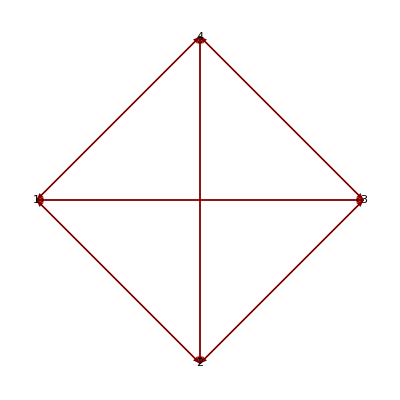

```mathematica
G = Graph[G]; 
GraphPlot[G, VertexLabeling-> True, DirectedEdges->True]
```

### Exemplo 2:

```mathematica
(* Creates a DGProblem with complete graph *)
x = {{0, 0, 0}, {1, 0, 0}, {0, 1, 0}, {1, 1, 1}, {0, 1, 1}};
P = DGProblem[x];
DGPrintGraph[P["G"]]
DGPrintDistanceMatrix[x]
```

| i | j | dij | lij | uij
1 | 1 | 2 | 1. | 1. | 1.
2 | 1 | 3 | 1. | 1. | 1.
3 | 1 | 4 | 1.73205 | 1.73205 | 1.73205
4 | 1 | 5 | 1.41421 | 1.41421 | 1.41421
5 | 2 | 3 | 1.41421 | 1.41421 | 1.41421
6 | 2 | 4 | 1.41421 | 1.41421 | 1.41421
7 | 2 | 5 | 1.73205 | 1.73205 | 1.73205
8 | 3 | 4 | 1.41421 | 1.41421 | 1.41421
9 | 3 | 5 | 1. | 1. | 1.
10 | 4 | 5 | 1. | 1. | 1.

| i | j | dij
1 | 1 | 2 | 1.
2 | 1 | 3 | 1.
3 | 1 | 4 | 1.73205
4 | 1 | 5 | 1.41421
5 | 2 | 3 | 1.41421
6 | 2 | 4 | 1.41421
7 | 2 | 5 | 1.73205
8 | 3 | 4 | 1.41421
9 | 3 | 5 | 1.
10 | 4 | 5 | 1.

### Exemplo 3:

```mathematica
(* Creates a DGProblem with specific edges *)
x = {{0, 0, 0}, {1, 0, 0}, {0, 1, 0}, {1, 1, 1}, {0, 1, 1}};
eij = {1 <-> 2, 2 <-> 3, 3 <-> 4, 4 <-> 5};
P = DGProblem[x, eij]; 
DGPrintGraph[P["G"]]
```

| i | j | dij | lij | uij
1 | 1 | 2 | 1. | 1. | 1.
2 | 2 | 3 | 1.41421 | 1.41421 | 1.41421
3 | 3 | 4 | 1.41421 | 1.41421 | 1.41421
4 | 4 | 5 | 1. | 1. | 1.

### Exemplo 4:

```mathematica
(* Creates a DGProblem with inexact distances *)
x = {{0, 0, 0}, {1, 0, 0}, {0, 1, 0}, {1, 1, 1}, {0, 1, 1}};
eij = {1<->2, 2<->3, 3<->4, 4<->5};
dijEps = {0, 0.1, 0, 0.2};
P = DGProblem[x, eij, dijEps];
DGPrintGraph[P["G"]]
```

| i | j | dij | lij | uij
1 | 1 | 2 | 1. | 1. | 1.
2 | 2 | 3 | 1.41421 | 1.27279 | 1.55563
3 | 3 | 4 | 1.41421 | 1.41421 | 1.41421
4 | 4 | 5 | 1. | 0.8 | 1.2

Plot Routines
DGPlot3DBackbone, DGPlotAdjacencyMatrix

## Source Code

```mathematica
ClearAll[
DGPlot3DBackbone,
DGPlotAdjacencyMatrix
]

DGPlot3DBackbone[X_,r_,d_]:=Module[{objs={},single,k,Y},
(* Plots the points using the coordinates of X["Points"] property *)
single=Length[X[[1]][[1]]]==0;
If[single,Y={X},Y=X];
For[k=1,k≤Length[Y],k++,
objs=Union[objs,Table[{Red,Sphere[Y[[k]][[i]],r]},{i,3}]];
objs=Union[objs,Table[{Blue,Sphere[Y[[k]][[i]],r]},{i,3,Length[Y[[k]]]}]];
AppendTo[objs,{LightGray,Tube[Y[[k]],d]}];
];
Graphics3D[
objs,
 Axes->False,
Boxed->False]
]

DGPlotAdjacencyMatrix[G_,DiagonalCovering_:False]:=Module[
{i,j,n,ei,ej,edges,primitives,add},
n=Max[VertexList[G]];
edges=EdgeList[G];
(* inverting edges position *)
edges=Table[{edges[[i]][[2]],n-edges[[i]][[1]]+1},{i,Length[edges]}];
primitives={
{PointSize[Medium],Point[edges]},
{Red,Dashed,Line[{{1,n},{n,1}}]}
};
(* Plot diagonal covering *)
If[DiagonalCovering,
For[i=1,i≤Length[edges],i++,
add=True;
ei=edges[[i]];
For[j=1,j≤Length[edges],j++,
ej=edges[[j]];
If[(ej[[1]]==ei[[1]]&&ej[[2]]>ei[[2]]),add=False];
If[(ej[[2]]==ei[[2]]&&ej[[1]]>ei[[1]]),add=False];
];
If[add,
PrependTo[primitives,
{Opacity[0.2],Red,Triangle[{{ei[[1]],n+1-ei[[1]]},ei,{n+1-ei[[2]],ei[[2]]}}]}]
];
];
];
Graphics[primitives,
Axes->True,
GridLines->Automatic,
Ticks->{Automatic,Table[{i,n+1-i},{i,n}]},
AxesOrigin->{1,1}
]
];
```

## Examples

### Exemplo 1:

```mathematica
(* Plot a simple a backbone *)
x=DGRandom3DBackbone[7];
DGPlot3DBackbone[x["Points"],0.1,0.04]
```

-Graphics3D-

### Exemplo 2:

```mathematica
(* Plot a simple a backbone *)
x=DGRandom3DBackbone[50];
DGPlot3DBackbone[x["Points"],0.1,0.04]
```

-Graphics3D-

### Exemplo 3:

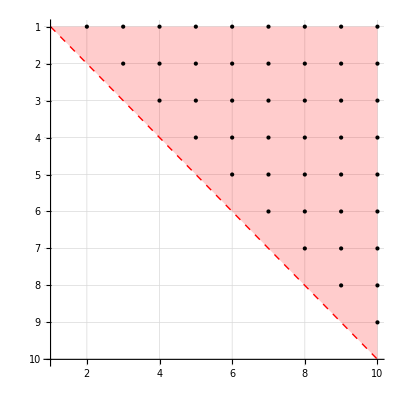

```mathematica
(* Plot adjacency matrix *)
P=DGRandomMDGP[10];
DGPlotAdjacencyMatrix[P["G"],True]
```

### Exemplo 4:

| i | j | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 2.77158 | 2.77158 | 2.77158
4 | 1 | 5 | 3.45253 | 3.45253 | 3.45253
5 | 2 | 3 | 1.526 | 1.526 | 1.526
6 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
7 | 2 | 5 | 3.03996 | 3.03996 | 3.03996
8 | 3 | 4 | 1.526 | 1.526 | 1.526
9 | 3 | 5 | 2.49139 | 2.49139 | 2.49139
10 | 4 | 5 | 1.526 | 1.526 | 1.526

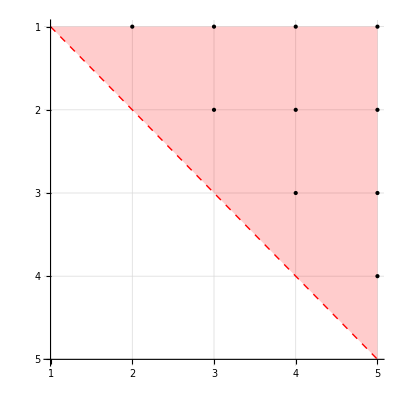

```mathematica
P=DGRandomMDGP[5];
DGPrintGraph[P["G"]]
DGPlotAdjacencyMatrix[P["G"],True]
```

### Exemplo 5:

| i | j | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 2.90434 | 2.90434 | 2.90434
4 | 2 | 3 | 1.526 | 1.526 | 1.526
5 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
6 | 2 | 5 | 3.83711 | 3.83711 | 3.83711
7 | 2 | 10 | 2.75737 | 2.75737 | 2.75737
8 | 3 | 4 | 1.526 | 1.526 | 1.526
9 | 3 | 5 | 2.49139 | 2.49139 | 2.49139
10 | 3 | 6 | 3.83633 | 3.83633 | 3.83633
11 | 3 | 9 | 2.59697 | 2.59697 | 2.59697
12 | 3 | 10 | 2.9989 | 2.9989 | 2.9989
13 | 4 | 5 | 1.526 | 1.526 | 1.526
14 | 4 | 6 | 2.49139 | 2.49139 | 2.49139
15 | 4 | 7 | 3.03573 | 3.03573 | 3.03573
16 | 4 | 8 | 2.64565 | 2.64565 | 2.64565
17 | 4 | 9 | 1.5221 | 1.5221 | 1.5221
18 | 4 | 10 | 2.43561 | 2.43561 | 2.43561
19 | 5 | 6 | 1.526 | 1.526 | 1.526
20 | 5 | 7 | 2.49139 | 2.49139 | 2.49139
21 | 5 | 8 | 2.93001 | 2.93001 | 2.93001
22 | 5 | 9 | 2.37749 | 2.37749 | 2.37749
23 | 6 | 7 | 1.526 | 1.526 | 1.526
24 | 6 | 8 | 2.49139 | 2.49139 | 2.49139
25 | 6 | 9 | 2.79911 | 2.79911 | 2.79911
26 | 7 | 8 | 1.526 | 1.526 | 1.526
27 | 7 | 9 | 2.49139 | 2.49139 | 2.49139
28 | 7 | 10 | 3.83547 | 3.83547 | 3.83547
29 | 8 | 9 | 1.526 | 1.526 | 1.526
30 | 8 | 10 | 2.49139 | 2.49139 | 2.49139
31 | 9 | 10 | 1.526 | 1.526 | 1.526

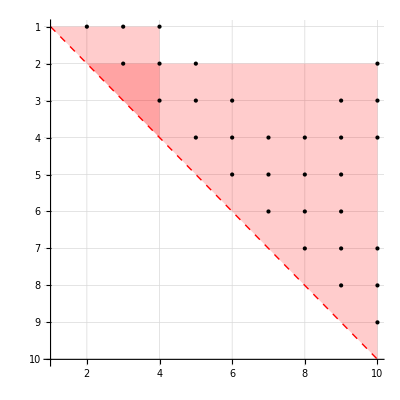

```mathematica
P=DGRandomMDGP[10,0,3,0]; (* DGRandomMDGP[numberOfAtoms_,dijEps_:0.0,dijMax_:Infinity,seed_:0]:=Module[...] *)
DGPrintGraph[P["G"]]
DGPlotAdjacencyMatrix[P["G"],True]
```

Solution Analysis 
DGRelativeResidue, DGLDME, DGRMSD

## Source Code

```mathematica
ClearAll[DGRelativeResidue,DGRMSD,DGLDME]
DGRelativeResidue[G_,X_,verbose_:False]:=Module[
{i,j,k,lij,uij, dij,numberOfEdges,E,error},
E=EdgeList[P["G"]];
numberOfEdges=Length[E];
error=Table[0,{i,numberOfEdges}];
For[k=1,k≤numberOfEdges,k++,
{i=E[[k]][[1]],j=E[[k]][[2]]};
{lij,uij}=DGEdgeDistanceBounds[G,i<->j];
dij=Norm[X[[i]]-X[[j]]];
error[[k]]=Max[Max[{0,lij-dij}]/lij,Max[{0,dij-uij}]/uij];
];
If[verbose,
Print["Solution Quality"];
Print["Number of nodes      : ",Length[X]];
Print["Number of edges      : ",Length[E]];
Print["Relative error bounds: ",{Min[error],Max[error]}];
Print["Mean relative error  : ",Mean[error]]];
Return[error]
];

DGRelativeResidue[G_,X_,nodes_,i_]:=
(* Calculates the relative residue of the nodes[[i]] considering only the nodes[[1;;i-1]] *)
Module[
(* local variables *)
{eij,j,k,V,Xi,Xj,Dij,Lij,Uij,errorDij,nid},
(* current position *)
Xi=X[[nodes[[i]]]];
(* indentifies which nodes has been already fixed *)
nid=Table[0,{k,i}];
For[k=1,k≤i,k++,
nid[[nodes[[k]]]]=k
];
(* considering only the precedent nodes *)
V= Select[AdjacencyList[G,nodes[[i]]],MemberQ[nid,#]&];
(*Print["V=",V];*)
errorDij=0.0;
For[k=1,k≤Length[V],k++,
(* neighbor index *)
j=V[[k]];
(* neighbor coordinate *)
Xj=X[[j]];
(* actual distance *)
Dij=EuclideanDistance[Xi,Xj];
(* distance bounds *)
{Lij,Uij}=DGEdgeDistanceBounds[G,i<->j];
(* error Dij *)
eij=Max[(Lij-Dij)/Lij,(Dij-Uij)/Uij];
(* update error *)
If[eij>errorDij,errorDij=eij];
];
Return[errorDij]
];

DGLDME[G_,X_]:=Module[
{i,j,k,E,ldme=0,lij,uij,dij},
E=EdgeList[G];
For[k=1,k≤Length[E],k++,
{lij,uij}=DGEdgeDistanceBounds[G,E[[k]]];
i=E[[k]][[1]];
j=E[[k]][[2]];
dij=Norm[X[[i]]-X[[j]],2];
ldme+=Max[lij-dij,dij-uij,0]^2
];
Return[Sqrt[ldme/Length[E]]]
];

DGRMSD[X_,Y_]:=Module[
{xc,yc,x,y,U,D,V,rmsd},
(* calculating centers *)
xc=Mean[X];
yc=Mean[Y];
(* translation *)
x=Table[X[[i]]-xc,{i,Length[X]}];
y=Table[Y[[i]]-yc,{i,Length[Y]}];
(* svd *)
V=Transpose[x].y;
{U,D,V}=SingularValueDecomposition[V];
V=U.Transpose[V];
x=x.V;
rmsd=Norm[x-y,"Frobenius"]/Sqrt[Length[x]];
Return[{rmsd,V,x,y}]
]
```

## Examples

### Exemplo 1:

```mathematica
(* DGRMSD *)
X={{0.814700,0.097500,0.157600},{0.905800,0.278500,0.970600},{0.127000,0.546900,0.957200},{0.913400,0.957500,0.485400},{0.632400,0.964900,0.800300}};
Y={{6.167723,5.509229,5.376972},{5.921716,5.625914,6.161379},{5.265461,5.705450,6.339958},{5.936486,6.432611,5.883000},{5.680966,5.982123,5.893736}};
{MatrixForm[X],MatrixForm[Y]}
{rmsd,Q,x,y}=DGRMSD[X,Y];
{rmsd,MatrixForm[Q],MatrixForm[x],MatrixForm[y]}
```

{(0.8147 | 0.0975 | 0.1576
0.9058 | 0.2785 | 0.9706
0.127 | 0.5469 | 0.9572
0.9134 | 0.9575 | 0.4854
0.6324 | 0.9649 | 0.8003),(6.16772 | 5.50923 | 5.37697
5.92172 | 5.62591 | 6.16138
5.26546 | 5.70545 | 6.33996
5.93649 | 6.43261 | 5.883
5.68097 | 5.98212 | 5.89374)}

{0.190378,(0.956675 | 0.276543 | 0.091089
-0.283739 | 0.955674 | 0.0786132
-0.0653114 | -0.101053 | 0.992735),(0.297687 | -0.360831 | -0.537546
0.280385 | -0.244816 | 0.292075
-0.539953 | -0.202332 | 0.228932
0.126686 | 0.455218 | -0.135529
-0.164806 | 0.35276 | 0.152068),(0.373253 | -0.341836 | -0.554037
0.127246 | -0.225151 | 0.23037
-0.529009 | -0.145615 | 0.408949
0.142016 | 0.581546 | -0.048009
-0.113504 | 0.131058 | -0.037273)}

### Exemplo 2:

```mathematica
(* Check relative error *)
x = {{0, 0, 0}, {1, 0, 0}, {0, 1, 0}, {1, 1, 1}, {0, 1, 1}};
P = DGProblem[x];
DGRelativeResidue[P["G"],x,True]
DGRelativeResidue[P["G"],x+RandomReal[0.1,Length[x]],True]
```

Solution Quality

Number of nodes      : 5

Number of edges      : 10

Relative error bounds: {0.,0.}

Solution Quality

Number of nodes      : 5

Number of edges      : 10

Relative error bounds: {0.,0.}

Mean relative error  : 0.

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

Solution Quality

Number of nodes      : 5

Number of edges      : 10

Relative error bounds: {0.000352625,0.0990765}

Mean relative error  : 0.0393882

{0.0990765,0.074296,0.0411513,0.0637284,0.000352625,0.0496252,0.00917898,0.028395,0.00690705,0.0211708}

Mean relative error  : 0.

### Exemplo 3:

```mathematica
x = {{0, 0, 0}, {1, 0, 0}, {0, 1, 0}, {1, 1, 1}, {0, 1, 1}};
P = DGProblem[x];
x[[4]]+=0.1;
DGRelativeResidue[P["G"],x,{1,2,3,4,5},4]
```

0.10227

General Methods
DGNSolve, DGAllEdgesSolver, DGOptSolver

## DGNSolve - Nonlinear equations

### Source Code

```mathematica
ClearAll[DGNSolve]
DGNSolve[G_]:=Module[{k,i,j,d,d12,eqs,xi,xj,x,n},
{i,j,d}=DGGraphGetIJD[G];
eqs=Table[0,{k,Length[i]}];
n=Max[i,j];
x=Table[Symbol[StringJoin["x",ToString[xi],ToString[xj]]],{xi,n},{xj,3}];
For[k=1,k≤Length[i],k++,
xi=x[[i[[k]]]];
xj=x[[j[[k]]]];
eqs[[k]]=(xi[[1]]-xj[[1]])^2+(xi[[2]]-xj[[2]])^2+(xi[[3]]-xj[[3]])^2==d[[k]]^2
];
(* set some points *)
d12=DGEdgeWeight[G,1<->2];
eqs=Join[eqs,
{x[[1]][[1]]==0,x[[1]][[2]]==0,x[[1]][[3]]==0,
x[[2]][[1]]==d12,x[[2]][[2]]==0,x[[2]][[3]]==0}
];
Print["eqs=",TableForm[eqs]];
x=Flatten[x];
Quiet[x=NSolve[eqs,x,Reals]];
x=ArrayReshape[x,{n,3}];
Print["x=",TableForm[x]];
(* convert relations to scalar matrix *)
If[Length[x[[1]][[1]]]>1,x=Table[x[[i]][[j]][[2]],{i,n},{j,3}]];
Return[x]
];
```

### Examples

#### Exemplo 1: 5 points and 4 constraints

```mathematica
x={{0,0,0},{1,0,0},{0,1,0},{0,0,1},{1,1,0}};
eij={{1,2},{1,3},{2,3},{2,5}};
P=DGProblem[x,eij];
DGPrintGraph[P["G"]];
x=DGNSolve[P["G"]];
TableForm[x,TableHeadings->{Table[i,{i,Length[x]}],{"x","y","z"}}]
DGRelativeResidue[P["G"],x,True];
```

| i | j | dij | lij | uij
1 | 1 | 2 | 1. | 1. | 1.
2 | 1 | 3 | 1. | 1. | 1.
3 | 2 | 3 | 1.41421 | 1.41421 | 1.41421
4 | 2 | 5 | 1. | 1. | 1.

eqs=(x11-x21)^2+(x12-x22)^2+(x13-x23)^2==1.
(x11-x31)^2+(x12-x32)^2+(x13-x33)^2==1.
(x21-x31)^2+(x22-x32)^2+(x23-x33)^2==2.
(x21-x51)^2+(x22-x52)^2+(x23-x53)^2==1.
x11==0
x12==0
x13==0
x21==1.
x22==0
x23==0

x=0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0

| x | y | z
1 | 0 | 0 | 0
2 | 0 | 0 | 0
3 | 0 | 0 | 0
4 | 0 | 0 | 0
5 | 0 | 0 | 0

Solution Quality

Number of nodes      : 5

Number of edges      : 4

Relative error bounds: {1.,1.}

Mean relative error  : 1.

#### Exemplo 2: 5 points and 4 constraints (failed)

```mathematica
x={
{0.732761,0.169653,0.656641},
{0.246863,0.660452,0.742898},
{0.426759,0.729058,0.897434},
{0.100975,0.670080,0.241258},
{0.204643,0.236955,0.655968}
};
eij={{1,2},{1,3},{2,3},{2,5}};
P=DGProblem[x,eij];
DGPrintGraph[P["G"]];
x=DGNSolve[P["G"]];
DGRelativeResidue[P["G"],x,True];
```

| i | j | dij | lij | uij
1 | 1 | 2 | 0.696003 | 0.696003 | 0.696003
2 | 1 | 3 | 0.681581 | 0.681581 | 0.681581
3 | 2 | 3 | 0.246882 | 0.246882 | 0.246882
4 | 2 | 5 | 0.434384 | 0.434384 | 0.434384

eqs=(x11-x21)^2+(x12-x22)^2+(x13-x23)^2==0.484421
(x11-x31)^2+(x12-x32)^2+(x13-x33)^2==0.464552
(x21-x31)^2+(x22-x32)^2+(x23-x33)^2==0.0609507
(x21-x51)^2+(x22-x52)^2+(x23-x53)^2==0.188689
x11==0
x12==0
x13==0
x21==0.696003
x22==0
x23==0

x=0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0

Solution Quality

Number of nodes      : 5

Number of edges      : 4

Relative error bounds: {1.,1.}

Mean relative error  : 1.

#### Exemplo 3: 5 points and all constraints

```mathematica
x={{0,0,0},{1,0,0},{0,1,0},{0,0,1},{1,1,0}};
P=DGProblem[x];
DGPrintGraph[P["G"]];
x=DGNSolve[P["G"]];
TableForm[x,TableHeadings->{Table[i,{i,Length[x]}],{"x","y","z"}}]
DGRelativeResidue[P["G"],x,True];
```

| i | j | dij | lij | uij
1 | 1 | 2 | 1. | 1. | 1.
2 | 1 | 3 | 1. | 1. | 1.
3 | 1 | 4 | 1. | 1. | 1.
4 | 1 | 5 | 1.41421 | 1.41421 | 1.41421
5 | 2 | 3 | 1.41421 | 1.41421 | 1.41421
6 | 2 | 4 | 1.41421 | 1.41421 | 1.41421
7 | 2 | 5 | 1. | 1. | 1.
8 | 3 | 4 | 1.41421 | 1.41421 | 1.41421
9 | 3 | 5 | 1. | 1. | 1.
10 | 4 | 5 | 1.73205 | 1.73205 | 1.73205

eqs=(x11-x21)^2+(x12-x22)^2+(x13-x23)^2==1.
(x11-x31)^2+(x12-x32)^2+(x13-x33)^2==1.
(x11-x41)^2+(x12-x42)^2+(x13-x43)^2==1.
(x11-x51)^2+(x12-x52)^2+(x13-x53)^2==2.
(x21-x31)^2+(x22-x32)^2+(x23-x33)^2==2.
(x21-x41)^2+(x22-x42)^2+(x23-x43)^2==2.
(x21-x51)^2+(x22-x52)^2+(x23-x53)^2==1.
(x31-x41)^2+(x32-x42)^2+(x33-x43)^2==2.
(x31-x51)^2+(x32-x52)^2+(x33-x53)^2==1.
(x41-x51)^2+(x42-x52)^2+(x43-x53)^2==3.
x11==0
x12==0
x13==0
x21==1.
x22==0
x23==0

x=x11→0. | x12→0. | x13→0.
x21→1. | x22→0. | x23→0.
x31→0. | x32→-0.990292 | x33→0.139004
x41→0. | x42→-0.139004 | x43→-0.990292
x51→1. | x52→-0.990292 | x53→0.139004

| x | y | z
1 | 0. | 0. | 0.
2 | 1. | 0. | 0.
3 | 0. | -0.990292 | 0.139004
4 | 0. | -0.139004 | -0.990292
5 | 1. | -0.990292 | 0.139004

Solution Quality

Number of nodes      : 5

Number of edges      : 10

Relative error bounds: {0.,2.44249×10^-15}

Mean relative error  : 7.74916×10^-16

#### Exemplo 4: 5 points and all constraints (failed)

```mathematica
x={
{0.732761,0.169653,0.656641},
{0.246863,0.660452,0.742898},
{0.426759,0.729058,0.897434},
{0.100975,0.670080,0.241258},
{0.204643,0.236955,0.655968}
};
P=DGProblem[x];
DGPrintGraph[P["G"]];
x=DGNSolve[P["G"]];
DGRelativeResidue[P["G"],x,True];
```

| i | j | dij | lij | uij
1 | 1 | 2 | 0.696003 | 0.696003 | 0.696003
2 | 1 | 3 | 0.681581 | 0.681581 | 0.681581
3 | 1 | 4 | 0.90671 | 0.90671 | 0.90671
4 | 1 | 5 | 0.53239 | 0.53239 | 0.53239
5 | 2 | 3 | 0.246882 | 0.246882 | 0.246882
6 | 2 | 4 | 0.522512 | 0.522512 | 0.522512
7 | 2 | 5 | 0.434384 | 0.434384 | 0.434384
8 | 3 | 4 | 0.73497 | 0.73497 | 0.73497
9 | 3 | 5 | 0.591445 | 0.591445 | 0.591445
10 | 4 | 5 | 0.608546 | 0.608546 | 0.608546

eqs=(x11-x21)^2+(x12-x22)^2+(x13-x23)^2==0.484421
(x11-x31)^2+(x12-x32)^2+(x13-x33)^2==0.464552
(x11-x41)^2+(x12-x42)^2+(x13-x43)^2==0.822124
(x11-x51)^2+(x12-x52)^2+(x13-x53)^2==0.283439
(x21-x31)^2+(x22-x32)^2+(x23-x33)^2==0.0609507
(x21-x41)^2+(x22-x42)^2+(x23-x43)^2==0.273019
(x21-x51)^2+(x22-x52)^2+(x23-x53)^2==0.188689
(x31-x41)^2+(x32-x42)^2+(x33-x43)^2==0.540181
(x31-x51)^2+(x32-x52)^2+(x33-x53)^2==0.349807
(x41-x51)^2+(x42-x52)^2+(x43-x53)^2==0.370329
x11==0
x12==0
x13==0
x21==0.696003
x22==0
x23==0

x=0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0

Solution Quality

Number of nodes      : 5

Number of edges      : 10

Relative error bounds: {1.,1.}

Mean relative error  : 1.

## DGOptSolver - Optimization

### Source Code

```mathematica
ClearAll[DGOptSolverFobj,DGOptSolver]
```

```mathematica
DGOptSolverFobj[i_,j_,d_,x_]:=Module[{f=0,numberOfAtoms,ncols,nrows,k,y},
y=ArrayReshape[x,{Length[x]/3,3}];
For[k=1,k≤Length[d],k++,
f+=(d[[k]]^2-Norm[y[[i[[k]]]]-y[[j[[k]]]]]^2)^2
];
Return[f]
]
DGOptSolver[G_]:=Module[{numberOfAtoms,f,y,v,w,i,j,d},
{i,j,d}=DGGraphGetIJD[G];
numberOfAtoms=Max[{i,j}];
ClearAll[z];
y=Array[z,3*numberOfAtoms];
f:=DGOptSolverFobj[i,j,d,#]&;
{v,y}=NMinimize[f[y],y];
y=ArrayReshape[y,{Length[y]/3,3}];
y=Table[y[[iloc]][[jloc]][[2]],{iloc,Length[y]},{jloc,3}];
Return[y]
]
```

### Examples

#### Exemplo 1:

```mathematica
(* Example C: Solving an instance with 5 points using optimization based method *)
x=RandomReal[1,{5,3}];
eij={{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{4,5}};
P=DGProblem[x,eij];
y=DGOptSolver[P["G"]];
DGRelativeResidue[P["G"],y,True];
```

Solution Quality

Number of nodes      : 5

Number of edges      : 9

Relative error bounds: {7.37769×10^-10,2.3123×10^-6}

Mean relative error  : 3.6656×10^-7

#### Exemplo 2:

```mathematica
x={
{0.732761,0.169653,0.656641},
{0.246863,0.660452,0.742898},
{0.426759,0.729058,0.897434},
{0.100975,0.670080,0.241258},
{0.204643,0.236955,0.655968}
};
eij={{1,2},{1,3},{2,3},{2,5}};
P=DGProblem[x,eij];
DGPrintGraph[P["G"]];
x=DGOptSolver[P["G"]];
DGRelativeResidue[P["G"],x,True];
```

| i | j | dij | lij | uij
1 | 1 | 2 | 0.696003 | 0.696003 | 0.696003
2 | 1 | 3 | 0.681581 | 0.681581 | 0.681581
3 | 2 | 3 | 0.246882 | 0.246882 | 0.246882
4 | 2 | 5 | 0.434384 | 0.434384 | 0.434384

Solution Quality

Number of nodes      : 5

Number of edges      : 4

Relative error bounds: {2.43745×10^-9,1.75969×10^-8}

Mean relative error  : 8.90727×10^-9

#### Exemplo 3:

```mathematica
(* Example D: Solving an instance with 100 points using optimization based method *)
(* It can take a lot of time!!! *) 
(* For[k=1,k≤100,k++,
SeedRandom[k];
x=RandomReal[1,{7,3}];
eij=MDGAllPairs[Length[x]];
eij=RandomSample[eij,Round[0.50Length[eij]]];
{i,j,d}=MDGCreateInstanceFromSolutionAndPairs[x,eij];
y=MDGOptSolver[i,j,d];
f=CheckMDGSolution[i,j,d,y,False];
If[Or[f>0.01,Mod[k,10]==0],
Print["{Seed,Error}=",{k,f}];
];
]
*)
```

## DGAllEdgesSolver - Solver for complete distance matrices

### Source Code

```mathematica
ClearAll[DGAllEdgesSolver]
DGAllEdgesSolver[G_]:=Module[{numberOfAtoms,k,m,λ,v,x,i,j,d},
{i,j,d}=DGGraphGetIJD[G];
numberOfAtoms=Max[{i,j}];
(* creates distance matrix *)
m=Table[0,{iloc,numberOfAtoms},{jloc,numberOfAtoms}];
For[k=1,k≤Length[i],k++,
m[[i[[k]]]][[j[[k]]]]=d[[k]];
m[[j[[k]]]][[i[[k]]]]=d[[k]];
];
(* λ:eigenvalues and v:eigenvectors *)
m=Table[(m[[1]][[iloc]]^2+m[[1]][[jloc]]^2-m[[iloc]][[jloc]]^2)/2,{iloc,numberOfAtoms},{jloc,numberOfAtoms}];
{λ,v}=Eigensystem[m,3];
(* getting solution *)
x=Table[Sqrt[λ[[jloc]]]v[[jloc]][[iloc]],{iloc,numberOfAtoms},{jloc,3}];
Return[x]
]
```

### Examples

#### Exemplo 1: 5 points and 4 constraints where DGNSolve fails

```mathematica
(*x={
{0.732761,0.169653,0.656641},
{0.246863,0.660452,0.742898},
{0.426759,0.729058,0.897434},
{0.100975,0.670080,0.241258},
{0.204643,0.236955,0.655968}
};*)
x={{0,0,0},
{-1.526000000000000,0,0},
{-2.033755510908970, 1.439048415148556,0},
{-3.559719882819027 ,1.439060986205111,0.010427631711570},
{-4.076155173310602 ,0.764476592552454,-1.257210521144031},
{-3.578831769689775 ,1.531380885110071,-2.479177475798574},
{-4.053530057464236 ,2.979379151615945,-2.397700142877220}
}
P=DGProblem[x];
DGPrintGraph[P["G"]];
x=DGAllEdgesSolver[P["G"]];
DGRelativeResidue[P["G"],x,True];
```

{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-3.55972,1.43906,0.0104276},{-4.07616,0.764477,-1.25721},{-3.57883,1.53138,-2.47918},{-4.05353,2.97938,-2.3977}}

| i | j | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 3.83961 | 3.83961 | 3.83961
4 | 1 | 5 | 4.33359 | 4.33359 | 4.33359
5 | 1 | 6 | 4.61514 | 4.61514 | 4.61514
6 | 1 | 7 | 5.57286 | 5.57286 | 5.57286
7 | 2 | 3 | 1.526 | 1.526 | 1.526
8 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
9 | 2 | 5 | 2.9442 | 2.9442 | 2.9442
10 | 2 | 6 | 3.56449 | 3.56449 | 3.56449
11 | 2 | 7 | 4.58411 | 4.58411 | 4.58411
12 | 3 | 4 | 1.526 | 1.526 | 1.526
13 | 3 | 5 | 2.49139 | 2.49139 | 2.49139
14 | 3 | 6 | 2.92269 | 2.92269 | 2.92269
15 | 3 | 7 | 3.493 | 3.493 | 3.493
16 | 4 | 5 | 1.526 | 1.526 | 1.526
17 | 4 | 6 | 2.49139 | 2.49139 | 2.49139
18 | 4 | 7 | 2.90095 | 2.90095 | 2.90095
19 | 5 | 6 | 1.526 | 1.526 | 1.526
20 | 5 | 7 | 2.49139 | 2.49139 | 2.49139
21 | 6 | 7 | 1.526 | 1.526 | 1.526

Solution Quality

Number of nodes      : 7

Number of edges      : 21

Relative error bounds: {0.,1.74609×10^-15}

Mean relative error  : 6.98646×10^-16

#### Exemplo 2: 100 points all constraints

```mathematica
x=RandomReal[1,{100,3}];
P=DGProblem[x];
tElapsed=Timing[x=DGAllEdgesSolver[P["G"]]][[1]]
DGRelativeResidue[P["G"],x,True];
```

0.343202

Solution Quality

Number of nodes      : 100

Number of edges      : 4950

Relative error bounds: {0.,5.79117×10^-15}

Mean relative error  : 2.94492×10^-16

Intersection of spheres
DGIntersect3Spheres, DGIntersect4Spheres, geraEsferas

## Source Code

```mathematica
ClearAll[DGIntersect3Spheres,DGIntersect4Spheres, geraEsferas];
DGIntersect3Spheres[a_,ra_,b_,rb_,c_,rc_]:=
(* Gets the 2 solutions of {||x-a||=ra,||x-b||=rb,||x-c||=rc};
   Input;
   a,b,c: sphere centers;
   ra,rb,rc: respective sphere radius;
   Output;   
   x: the two intersections (x[[1]]: positive chirality and x[[2]]: negative chirality);
 *)
Module[{n,A,x,p,dp,u,v,w,du,dv,dw,dpu,AbsCos,error},
(* select the most perpendicular vertex angle (stability) *)
(*Print["a=",a,"  ra=",ra,"  b=",b,"  rb=",rb,"  c=",c,"  rc=",rc];*)
AbsCos[u_,v_]:=Dot[u,v]/(Norm[u]*Norm[v]);
{u,v,w,du,dv,dw}=MinimalBy[{
{AbsCos[b-a,c-a],{a,b,c,ra,rb,rc}},
{AbsCos[c-b,a-b],{b,c,a,rb,rc,ra}},
{AbsCos[a-c,b-c],{c,a,b,rc,ra,rb}}
},First][[1]][[2]];
(* normal to the plane (u,v,w) *)
n=Normalize[Cross[v-u,w-u]];
A={v-u,w-u,n};
x={(Dot[v,v]-Dot[u,u]-dv^2+du^2)/2,(Dot[w,w]-Dot[u,u]-dw^2+du^2)/2,Dot[n,u]};
p=LinearSolve[A,x];
(* select the factor with minimal canceling effect (stability) *)
{u,du}=MaximalBy[{
{Abs[(ra-Norm[p-a])/ra],{a,ra}},
{Abs[(rb-Norm[p-b])/rb],{b,rb}},
{Abs[(rc-Norm[p-c])/rc],{c,rc}}
},First][[1]][[2]];
dpu=Norm[p-u];
dp=N[Sqrt[(du+dpu)*(du-dpu)]];
(*dp=Re[dp];*)
x={p+dp*n,p-dp*n};
(*Print["a=",a,"  ra=",ra,"  b=",b,"  rb=",rb,"  c=",c,"  rc=",rc];
Print["p=",p,"  dp=",dp,"  x=",x];*)
(* calculating max relative errors of each solution *)
error=Table[Max[Abs[{(Norm[a-x[[i]]]-ra)/ra,(Norm[b-x[[i]]]-rb)/rb,(Norm[c-x[[i]]]-rc)/rc}]],{i,2}];
Return[{x,error}];
];

DGIntersect4Spheres[a_,ra_,b_,rb_,c_,rc_,d_,rd_]:=
Module[{x,error,errd1,errd2},
{x,error}=DGIntersect3Spheres[a,ra,b,rb,c,rc];
errd1=Abs[N[Norm[x[[1]]-d]]-rd];
errd2=Abs[N[Norm[x[[2]]-d]]-rd];
If[errd1<errd2,
x=x[[1]];
error=Max[error[[1]],errd1],
x=x[[2]];
error=Max[error[[2]],errd2]
];
Return[{x,error}]
];

(* módulo que gera matriz n×m de rank k, cujas colunas são os centros das m esferas;gera vetor com os raios; obs: m = qtde de esferas no ℝ^n *)
geraEsferas[m_,n_]:=Module[{A,i,j,d,λ,u,v,Amin,Amax,xstar,di,k},
k=Min[{m-1,n}];
A=Table[0,{i,n},{j,m}];d=Table[0,{i,m},{j,1}];
For[i=1,i≤k,i++,
λ=RandomReal[{0,10}];u=RandomReal[{0,1},n];
v=RandomReal[{0,1},m];A=A+λ*Outer[Times,u,v];
];
Amin=Min[A];Amax=Max[A]; xstar=RandomReal[{Amin,Amax},n];
For[i=1,i≤m,i++,
di=Norm[xstar-A[[;;,i]]]; d[[i,1]]=di;
];
Return[{A,d}];
];
```

## Examples

### Exemplo 1 (gera 3 esferas L.I. em um espaço 3D e encontra a interseção):

```mathematica
quantidade = 3; dimensao = 3;
```

```mathematica
{centros,raios} = geraEsferas[quantidade, dimensao];
Print[">> centros [obs: coluna_i = centro_i]: ", MatrixForm[centros]];
Print[ "   raios: ", MatrixForm[raios]];
```

>> centros [obs: coluna_i = centro_i]: (0.201706 | 2.47408 | 2.55939
0.0969673 | 1.16782 | 1.17616
0.0706282 | 0.865793 | 0.894877)

raios: (1.75179
1.13737
1.2015)

```mathematica
{solucao,erroSolucao} = DGIntersect3Spheres[centros[[;;,1]],raios[[1,1]],centros[[;;,2]],raios[[2,1]],centros[[;;,3]],raios[[3,1]]];
Print[">> Solução: ", Style[solucao,Red], ",  erro: ", Style[erroSolucao,Red]];
```

>> Solução: {{1.92002,0.362798,0.283936},{1.69238,0.346621,0.956248}},  erro: {2.53506×10^-16,2.53506×10^-16}

### Exemplo 2 (gera 4 esferas L.I. em um espaço 3D e encontra a interseção):

```mathematica
quantidade = 4; dimensao = 3;
```

```mathematica
{centros,raios} = geraEsferas[quantidade, dimensao];
Print[">> centros [obs: coluna_i = centro_i]: ", MatrixForm[centros]];
Print[ "   raios: ", MatrixForm[raios]];
```

>> centros [obs: coluna_i = centro_i]: (4.02348 | 2.49865 | 3.02349 | 3.62822
3.44862 | 4.03009 | 3.52032 | 3.97524
7.92896 | 7.33881 | 7.15916 | 8.27678)

raios: (2.8058
2.66622
2.3443
3.07573)

```mathematica
{solucao,erroSolucao} = DGIntersect4Spheres[centros[[;;,1]],raios[[1,1]],centros[[;;,2]],raios[[2,1]],centros[[;;,3]],raios[[3,1]],centros[[;;,4]],raios[[4,1]]];
Print[">> Solução: ", Style[solucao,Red], ",  erro: ", Style[erroSolucao,Red]];
```

>> Solução: {4.14928,4.32146,5.26535},  erro: 6.66246×10^-16